# Prakhar Khugshal || BSc(Hons) Computer Science || Semester IV || 20211441

## Regular Falsi

## Q1

x0=1

x1=2

Nmax=20

epsilon=1/1000000

f(x):=Cos[x]

1the iteration value is:a16

Estimated error is: 1.

2the iteration value is:a16

Estimated error is: 0.435095624108422

3the iteration value is:a16

Estimated error is: 0.00607419864344

4the iteration value is:a16

Estimated error is: 0.00018224876197

5the iteration value is:a16

Estimated error is: 0.0001822477401

6the iteration value is:a16

Estimated error is: 0.0001822477401

7the iteration value is:a16

Estimated error is: 0.0001822477401

8the iteration value is:a16

Estimated error is: 0.00018224774

9the iteration value is:a16

Estimated error is: 0.00018224774

10the iteration value is:a16

Estimated error is: 0.00018224774

11the iteration value is:a16

Estimated error is: 0.00018224774

12the iteration value is:a16

Estimated error is: 0.00018224774

13the iteration value is:a16

Estimated error is: 0.00018224774

14the iteration value is:a16

Estimated error is: 0.0001822477

15the iteration value is:a16

Estimated error is: 0.0001822477

16the iteration value is:a16

Estimated error is: 0.0001822477

17the iteration value is:a16

Estimated error is: 0.0001822477

18the iteration value is:a16

Estimated error is: 0.000182248

19the iteration value is:a16

Estimated error is: 0.000182248

20the iteration value is:a16

Estimated error is: 0.000182248

Root is: 1.57079633

Estimated eror is:0.00018225

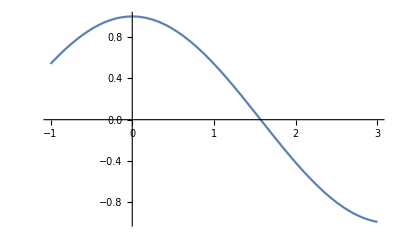

```mathematica
x0 = Input["Enter first guess: "];
x1 =Input ["Enter scond guess: "];
Nmax = Input["Enter maximum of iterations : " ];
eps= Input["Enter the value of covergence parameter: "];
Print["x0=",x0];
Print["x1=",x1];
Print["Nmax=",Nmax];
Print["epsilon=",eps];
f[x_]:=Cos[x];
Print["f(x):=",f[x]];If[N[f[x0]*f[x1]]>0,
Print["These values does not satisfy the IVP so change the values "],
For[i=1,i≤ Nmax,i++,a=N[x1-f[x1]*(x1-x0)/(f[x1]-f[x0]),16];
If[Abs[x1-x0/2]<eps,Return[N[a,16]],Print[i,"the iteration value is:",N[a16]];
Print["Estimated error is: ",N[x1-x0,16]];
If[f[a]*f[x1]>0,x1=a,x0=a]]];
Print["Root is: ",N[a,16]];
Print["Estimated eror is:",N[x1-x0,16]]];
Plot[f[x],{x,-1,3}]
```

## Q2

x0=1

x1=2

Nmax=20

epsilon=1/1000000

f(x):=1-5 x+x^3

These values does not satisfy the IVP so change the values

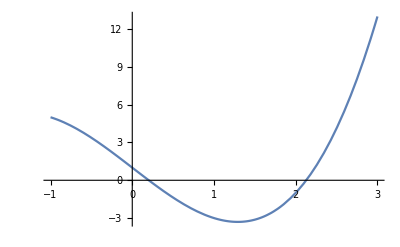

```mathematica
x0 = Input["Enter first guess: "];
x1 =Input ["Enter scond guess: "];
Nmax = Input["Enter maximum of iterations : " ];
eps= Input["Enter the value of covergence parameter: "];
Print["x0=",x0];
Print["x1=",x1];
Print["Nmax=",Nmax];
Print["epsilon=",eps];
f[x_]:=x^3-5*x+1;
Print["f(x):=",f[x]];If[N[f[x0]*f[x1]]>0,
Print["These values does not satisfy the IVP so change the values "],
For[i=1,i≤ Nmax,i++,a=N[x1-f[x1]*(x1-x0)/(f[x1]-f[x0]),16];
If[Abs[x1-x0/2]<eps,Return[N[a,16]],Print[i,"the iteration value is:",N[a16]];
Print["Estimated error is: ",N[x1-x0,16]];
If[f[a]*f[x1]>0,x1=a,x0=a]]];
Print["Root is: ",N[a,16]];
Print["Estimated eror is:",N[x1-x0,16]]];
Plot[f[x],{x,-1,3}]
```

## Q3

```mathematica
x0 = Input["Enter first guess: "];
x1 =Input ["Enter scond guess: "];
Nmax = Input["Enter maximum of iterations : " ];
eps= Input["Enter the value of covergence parameter: "];
Print["x0=",x0];
Print["x1=",x1];
Print["Nmax=",Nmax];
Print["epsilon=",eps];
f[x_]:=Cos[x]-x*e^x;
Print["f(x):=",f[x]];If[N[f[x0]*f[x1]]>0,
Print["These values does not satisfy the IVP so change the values "],
For[i=1,i≤ Nmax,i++,a=N[x1-f[x1]*(x1-x0)/(f[x1]-f[x0]),16];
If[Abs[x1-x0/2]<eps,Return[N[a,16]],Print[i,"the iteration value is:",N[a16]];
Print["Estimated error is: ",N[x1-x0,16]];
If[f[a]*f[x1]>0,x1=a,x0=a]]];
Print["Root is: ",N[a,16]];
Print["Estimated eror is:",N[x1-x0,16]]];
Plot[f[x],{x,-1,3}]
```

x0=1

x1=2

Nmax=20

epsilon=1/1000000

f(x):=-e^x x+Cos[x]

-Graphics-